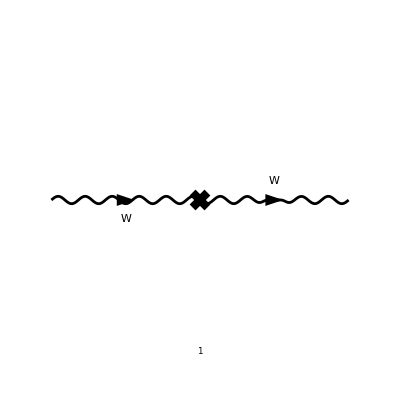

FeynArtsGraphics()(([1] | Null | Null
Null | Null | Null
Null | Null | Null))

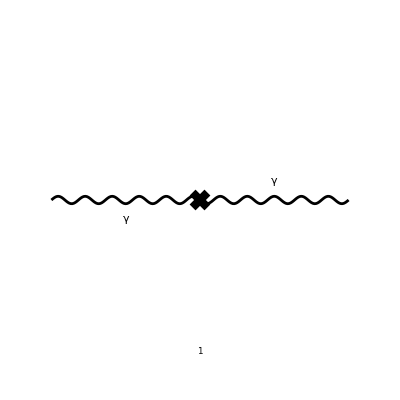

FeynArtsGraphics()(([1] | Null | Null
Null | Null | Null
Null | Null | Null))

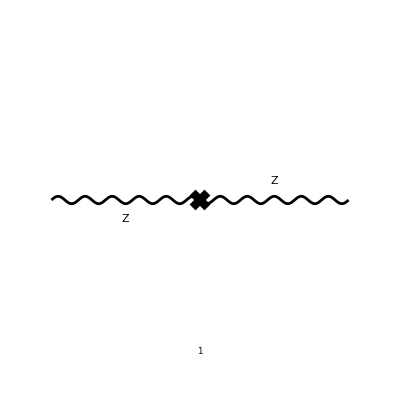

FeynArtsGraphics()(([1] | Null | Null
Null | Null | Null
Null | Null | Null))

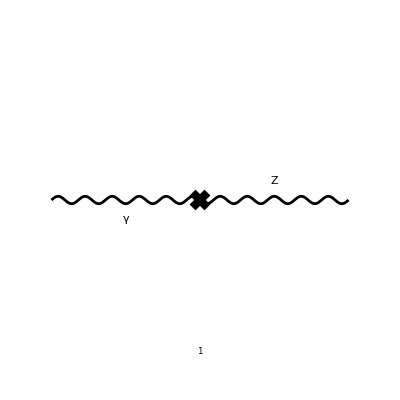

FeynArtsGraphics()(([1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
topoctself=CreateCTTopologies[1,1-> 1,SelfEnergiesOnly];
WctW=InsertFields[topoctself,process0, InsertionLevel-> {Particles}];
ActA=InsertFields[topoctself,process2, InsertionLevel-> {Particles}];
ZctZ=InsertFields[topoctself,process1, InsertionLevel->{Particles}];
ActZ= InsertFields[topoctself,process3,InsertionLevel-> {Particles}];
Paint[WctW,SheetHeader-> False]
Paint[ActA,SheetHeader-> False]
Paint[ZctZ,SheetHeader-> False]
Paint[ActZ, SheetHeader-> False]
```

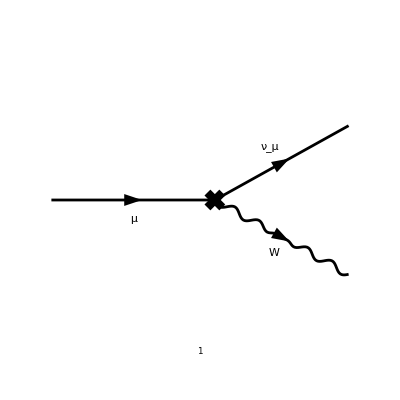

FeynArtsGraphics()(([1] | Null | Null
Null | Null | Null
Null | Null | Null))

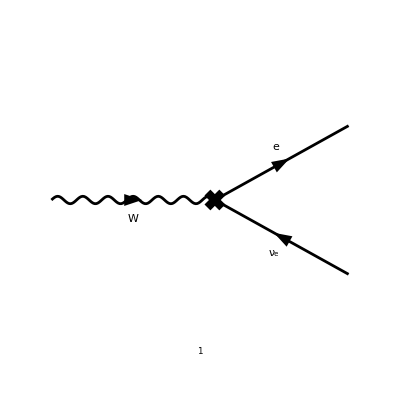

FeynArtsGraphics()(([1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
topovertex=CreateCTTopologies[1,1-> 2];
muctnu=DiagramExtract[InsertFields[topovertex,F[2,{2}]->{F[1,{2}], V[3]},InsertionLevel-> {Particles}],1];
ectnu=DiagramExtract[InsertFields[topovertex,V[3]-> {F[2,{1}],-F[1,{1}]},InsertionLevel-> {Particles}],1];
Paint[muctnu]
Paint[ectnu]
```

```mathematica
ampctww=FCFAConvert[CreateFeynAmp[WctW, Truncated-> True,PreFactor-> 1,GaugeRules-> {}],List-> False,SMP-> True,ChangeDimension-> D, IncomingMomenta-> {k},OutgoingMomenta-> {k},DropSumOver-> True,LorentzIndexNames-> {μ,ν}, UndoChiralSplittings-> True, FinalSubstitutions-> {SMP["m_mu"]-> 0,SMP["m_u"]-> 0,SMP["m_d"]-> 0,SMP["m_e"]-> 0,SMP["m_c"]-> 0,SMP["m_s"]-> 0,SMP["m_b"]->0}]//Contract//FCTraceFactor
ampctaa=FCFAConvert[CreateFeynAmp[ActA, Truncated-> True,PreFactor-> 1,GaugeRules-> {}],List-> False,SMP-> True,ChangeDimension-> D, IncomingMomenta-> {k},OutgoingMomenta-> {k},DropSumOver-> True,LorentzIndexNames-> {μ,ν}, UndoChiralSplittings-> True, FinalSubstitutions-> {SMP["m_mu"]-> 0,SMP["m_u"]-> 0,SMP["m_d"]-> 0,SMP["m_e"]-> 0,SMP["m_c"]-> 0,SMP["m_s"]-> 0,SMP["m_b"]->0}]//Contract//FCTraceFactor
ampctzz=FCFAConvert[CreateFeynAmp[ZctZ, Truncated-> True,PreFactor-> 1,GaugeRules-> {}],List-> False,SMP-> True,ChangeDimension-> D, IncomingMomenta-> {k},OutgoingMomenta-> {k},DropSumOver-> True,LorentzIndexNames-> {μ,ν}, UndoChiralSplittings-> True, FinalSubstitutions-> {SMP["m_mu"]-> 0,SMP["m_u"]-> 0,SMP["m_d"]-> 0,SMP["m_e"]-> 0,SMP["m_c"]-> 0,SMP["m_s"]-> 0,SMP["m_b"]->0}]//Contract//FCTraceFactor
ampctaz=FCFAConvert[CreateFeynAmp[ActZ, Truncated-> True,PreFactor-> 1,GaugeRules-> {}],List-> False,SMP-> True,ChangeDimension-> D, IncomingMomenta-> {k},OutgoingMomenta-> {k},DropSumOver-> True,LorentzIndexNames-> {μ,ν}, UndoChiralSplittings-> True, FinalSubstitutions-> {SMP["m_mu"]-> 0,SMP["m_u"]-> 0,SMP["m_d"]-> 0,SMP["m_e"]-> 0,SMP["m_c"]-> 0,SMP["m_s"]-> 0,SMP["m_b"]->0}]//Contract//FCTraceFactor
ampctvertex1=FCFAConvert[CreateFeynAmp[muctnu,Truncated-> True, PreFactor -> 1, GaugeRules-> {}], List-> False, SMP-> True, ChangeDimension-> D, IncomingMomenta-> {p1}, OutgoingMomenta-> {k,p2},DropSumOver-> True, LorentzIndexNames-> {μ,ν},UndoChiralSplittings-> True, FinalSubstitutions-> {SMP["m_mu"]-> 0,SMP["m_u"]-> 0,SMP["m_d"]-> 0,SMP["m_e"]-> 0,SMP["m_c"]-> 0,SMP["m_s"]-> 0,SMP["m_b"]->0}]//Contract//FCTraceFactor
ampctvertex2=FCFAConvert[CreateFeynAmp[ectnu,Truncated-> True, PreFactor -> 1, GaugeRules-> {}], List-> False, SMP-> True, ChangeDimension-> D, IncomingMomenta-> {k}, OutgoingMomenta-> {p3,p4},DropSumOver-> True, LorentzIndexNames-> {μ,ν},UndoChiralSplittings-> True, FinalSubstitutions-> {SMP["m_mu"]-> 0,SMP["m_u"]-> 0,SMP["m_d"]-> 0,SMP["m_e"]-> 0,SMP["m_c"]-> 0,SMP["m_s"]-> 0,SMP["m_b"]->0}]//Contract//FCTraceFactor
```

ⅈ g^μν (dMWsq1+dZW1 m_W^2)-ⅈ dZW1 k^2 g^μν+ⅈ dZW1 k^μ k^ν

ⅈ dZAA1 k^μ k^ν-ⅈ dZAA1 k^2 g^μν

ⅈ g^μν (dMZsq1+dZZZ1 m_Z^2)-ⅈ dZZZ1 k^2 g^μν+ⅈ dZZZ1 k^μ k^ν

-ⅈ k^2 (dZAZ1/2+dZZA1/2) g^μν-ⅈ (-dZAZ1/2-dZZA1/2) k^μ k^ν+1/2 ⅈ dZZA1 m_Z^2 g^μν

(ⅈ e γ^μ.(γ̄)^7 (1/2 Conjugate[dZfL1(1,2,2)]+1/2 dZfL1(2,2,2)-dSW1/(sin(θ_W))+dZe1+dZW1/2))/(√2 (sin(θ_W)))

-(ⅈ e γ^μ.(γ̄)^7 (1/2 Conjugate[dZfL1(2,1,1)]+1/2 dZfL1(1,1,1)-dSW1/(sin(θ_W))+dZe1+dZW1/2))/(√2 (sin(θ_W)))

```mathematica
transversewctw=ⅈ/(D-1)(Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]-Pair[LorentzIndex[μ,D],Momentum[k,D]]Pair[LorentzIndex[ν,D],Momentum[k,D]]/Pair[Momentum[k,D],Momentum[k,D]]). ampctww//Contract//FullSimplify

transverseacta=ⅈ/(D-1)(Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]-Pair[LorentzIndex[μ,D],Momentum[k,D]]Pair[LorentzIndex[ν,D],Momentum[k,D]]/Pair[Momentum[k,D],Momentum[k,D]]). ampctaa//Contract//FullSimplify
transversezctz=ⅈ/(D-1)(Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]-Pair[LorentzIndex[μ,D],Momentum[k,D]]Pair[LorentzIndex[ν,D],Momentum[k,D]]/Pair[Momentum[k,D],Momentum[k,D]]). ampctzz//Contract//FullSimplify
transverseactz=ⅈ/(D-1)(Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]-Pair[LorentzIndex[μ,D],Momentum[k,D]]Pair[LorentzIndex[ν,D],Momentum[k,D]]/Pair[Momentum[k,D],Momentum[k,D]]). ampctaz//Contract//FullSimplify
```

-dMWsq1+dZW1 k^2-dZW1 m_W^2

dZAA1 k^2

-dMZsq1+dZZZ1 k^2-dZZZ1 m_Z^2

1/2 (k^2 (dZAZ1+dZZA1)-dZZA1 m_Z^2)

```mathematica
transwCTw[k_]=-dMWsq1+dZW1  k^2 -dZW1 SMP["m_W"]^2;
dtranswCTw[k_]=D[transversewctw,Pair[Momentum[k,D],Momentum[k,D]]]/.Pair[Momentum[k,D],Momentum[k,D]]-> k^2;
transaCTa[k_]=dZAA1 k^2;
dtransaCTa[k_]=D[transverseacta,Pair[Momentum[k,D],Momentum[k,D]]]/.Pair[Momentum[k,D],Momentum[k,D]]-> k^2;
transaCTz[k_]=1/2(k^2(dZAZ1+dZZA1)-dZZA1 SMP["m_Z"]^2);
transzCTz[k_]=-dMZsq1+dZZZ1 k^2-dZZZ1 SMP["m_Z"]^2;
dtranszCTz[k_]=D[transversezctz,Pair[Momentum[k,D],Momentum[k,D]]]/.Pair[Momentum[k,D],Momentum[k,D]]-> k^2;
```

```mathematica
rule2={Solve[ΣWW[SMP["m_W"]]+transwCTw[SMP["m_W"]]==0,dMWsq1]//Flatten,
Solve[dΣWW[SMP["m_W"]]+dtranswCTw[SMP["m_W"]]==0,dZW1]//Flatten,
Solve[ΣZZ[SMP["m_Z"]]+transzCTz[SMP["m_Z"]]==0,dMZsq1]//Flatten,
Solve[dΣZZ[SMP["m_Z"]]+dtranszCTz[SMP["m_Z"]]==0,dZZZ1]//Flatten,
Solve[Πγγ[0]+dtransaCTa[0]==0,dZAA1]//Flatten,
Solve[ΣAZ[0]+transaCTz[0]==0,dZZA1]//Flatten,
Solve[ΣAZ[SMP["m_Z"]]+transaCTz[SMP["m_Z"]]==0,dZAZ1]//Flatten}//Flatten
```

{dMWsq1→-(3 π B_0(m_W^2,0,m_t^2) α m_t^4)/(8 (D-1) m_W^2 (sin(θ_W))^2)-(3 D π B_0(m_W^2,0,m_t^2) α m_t^2)/(8 (D-1) (sin(θ_W))^2)+(9 π B_0(m_W^2,0,m_t^2) α m_t^2)/(8 (D-1) (sin(θ_W))^2)+(3 π A_0(m_t^2) α m_t^2)/(8 (D-1) m_W^2 (sin(θ_W))^2)-(9 D π B_0(m_W^2,0,0) α m_W^2)/(8 (1-D) (sin(θ_W))^2)+(9 π B_0(m_W^2,0,0) α m_W^2)/(4 (1-D) (sin(θ_W))^2)+(3 D π B_0(m_W^2,0,m_t^2) α m_W^2)/(8 (D-1) (sin(θ_W))^2)-(3 π B_0(m_W^2,0,m_t^2) α m_W^2)/(4 (D-1) (sin(θ_W))^2)-(3 D π A_0(m_t^2) α)/(8 (D-1) (sin(θ_W))^2)+(3 π A_0(m_t^2) α)/(4 (D-1) (sin(θ_W))^2),dZW1→0,dMZsq1→((D-2) π B_0(m_Z^2,0,0) α (40 (4 (sin(θ_W))^2-3) (sin(θ_W))^2+63) m_Z^2)/(48 (D-1) (cos(θ_W))^2 (sin(θ_W))^2)-((2-D) π A_0(m_t^2) α (32 (sin(θ_W))^4-24 (sin(θ_W))^2+9))/(24 (1-D) (cos(θ_W))^2 (sin(θ_W))^2)+1/(48 (1-D) (cos(θ_W))^2 (sin(θ_W))^2)π B_0(m_Z^2,m_t^2,m_t^2) α (-128 m_t^2 (sin(θ_W))^4-32 D m_Z^2 (sin(θ_W))^4+64 m_Z^2 (sin(θ_W))^4+96 m_t^2 (sin(θ_W))^2+24 D m_Z^2 (sin(θ_W))^2-48 m_Z^2 (sin(θ_W))^2+18 D m_t^2-54 m_t^2-9 D m_Z^2+18 m_Z^2),dZZZ1→-((D-2) π DB0(m_Z^2,0,0) α (40 (4 (sin(θ_W))^2-3) (sin(θ_W))^2+63) m_Z^2)/(48 (D-1) (cos(θ_W))^2 (sin(θ_W))^2)-(π B_0(m_Z^2,m_t^2,m_t^2) α (-32 D (sin(θ_W))^4+64 (sin(θ_W))^4+24 D (sin(θ_W))^2-48 (sin(θ_W))^2-9 D+18))/(48 (1-D) (cos(θ_W))^2 (sin(θ_W))^2)-1/(48 (1-D) (cos(θ_W))^2 (sin(θ_W))^2)π DB0(m_Z^2,m_t^2,m_t^2) α (-128 m_t^2 (sin(θ_W))^4-32 D m_Z^2 (sin(θ_W))^4+64 m_Z^2 (sin(θ_W))^4+96 m_t^2 (sin(θ_W))^2+24 D m_Z^2 (sin(θ_W))^2-48 m_Z^2 (sin(θ_W))^2+18 D m_t^2-54 m_t^2-9 D m_Z^2+18 m_Z^2)-((D-2) π B_0(m_Z^2,0,0) α (40 (4 (sin(θ_W))^2-3) (sin(θ_W))^2+63))/(48 (D-1) (cos(θ_W))^2 (sin(θ_W))^2),dZAA1→-(2 π A_0(m_t^2) α D^2)/(9 (D-1) m_t^2)+(10 π B_0(m_Z^2,0,0) α D)/(3 (1-D))+(2 π A_0(m_t^2) α D)/(3 (D-1) m_t^2)-π^2 Δα-(20 π B_0(m_Z^2,0,0) α)/(3 (1-D))-(4 π A_0(m_t^2) α)/(9 (D-1) m_t^2),dZZA1→-1/(9 (D-1) (cos(θ_W)) m_Z^2 (sin(θ_W)))π (-16 B_0(0,m_t^2,m_t^2) α (sin(θ_W))^2 m_t^2+6 B_0(0,m_t^2,m_t^2) α m_t^2+8 D A_0(m_t^2) α (sin(θ_W))^2-16 A_0(m_t^2) α (sin(θ_W))^2-3 D A_0(m_t^2) α+6 A_0(m_t^2) α),dZAZ1→1/m_Z^2 2 (((2-D) π B_0(m_Z^2,0,0) α (21-44 (sin(θ_W))^2) m_Z^2)/(72 (1-D) (cos(θ_W)) (sin(θ_W)))+(3 (2-D) π B_0(m_Z^2,0,0) α (1-4 (sin(θ_W))^2) m_Z^2)/(8 (1-D) (cos(θ_W)) (sin(θ_W)))+(ⅈ ((8 ⅈ (2-D) π^3 A_0(m_t^2) α (3-8 (sin(θ_W))^2))/(9 (1-D) (cos(θ_W)) (sin(θ_W)))-(4 ⅈ π^3 B_0(m_Z^2,m_t^2,m_t^2) α (-4 m_t^2-D m_Z^2+2 m_Z^2) (3-8 (sin(θ_W))^2))/(9 (1-D) (cos(θ_W)) (sin(θ_W)))))/(16 π^2))}

```mathematica
rule3={SumOver[SUNFIndex[Col3],3]-> 3 ,DB0[z_,0,0]->(-(4-D))/(2z)B0[z,0,0],DB0[0,0,w_]-> (4-D)/D A0[w]/w,B0[0,0,x_]-> 1/x A0[x],B0[0,y_,y_]-> (D/2-1)A0[y]/y,DB0[0,s_,s_]-> -1/6(D/2-1)(D/2-2) A0[s]/s^2};


 dZAA1+2 π^2 δZe/.FCI[rule2]//FullSimplify
```

0

```mathematica
dZZA1/.FCI[rule2]/.FCI[rule3]//FullSimplify
```

0

```mathematica
Δrferm=Σd0/SMP["m_W"]^2-dMWsq1/SMP["m_W"]^2+Πγγ[0]+SMP["cos_W"]^2/SMP["sin_W"]^2(dMWsq1/SMP["m_W"]^2-dMZsq1/SMP["m_Z"]^2)/.FCI[rule2]/.FCI[rule3]//Expand
```

(3 π B_0(m_W^2,0,m_t^2) α m_t^4)/(8 (D-1) m_W^4 (sin(θ_W))^2)-(3 π B_0(m_W^2,0,m_t^2) α (cos(θ_W))^2 m_t^4)/(8 (D-1) m_W^4 (sin(θ_W))^4)+(8 π B_0(m_Z^2,m_t^2,m_t^2) α m_t^2)/(3 (1-D) m_Z^2)+(3 D π B_0(m_W^2,0,m_t^2) α m_t^2)/(8 (D-1) m_W^2 (sin(θ_W))^2)-(9 π B_0(m_W^2,0,m_t^2) α m_t^2)/(8 (D-1) m_W^2 (sin(θ_W))^2)-(2 π B_0(m_Z^2,m_t^2,m_t^2) α m_t^2)/((1-D) m_Z^2 (sin(θ_W))^2)-(3 π A_0(m_t^2) α m_t^2)/(8 (D-1) m_W^4 (sin(θ_W))^2)-(3 D π B_0(m_W^2,0,m_t^2) α (cos(θ_W))^2 m_t^2)/(8 (D-1) m_W^2 (sin(θ_W))^4)+(9 π B_0(m_W^2,0,m_t^2) α (cos(θ_W))^2 m_t^2)/(8 (D-1) m_W^2 (sin(θ_W))^4)-(3 D π B_0(m_Z^2,m_t^2,m_t^2) α m_t^2)/(8 (1-D) m_Z^2 (sin(θ_W))^4)+(9 π B_0(m_Z^2,m_t^2,m_t^2) α m_t^2)/(8 (1-D) m_Z^2 (sin(θ_W))^4)+(3 π A_0(m_t^2) α (cos(θ_W))^2 m_t^2)/(8 (D-1) m_W^4 (sin(θ_W))^4)+π^2 Δα-(10 D π B_0(m_Z^2,0,0) α)/(3 (1-D))-(10 D π B_0(m_Z^2,0,0) α)/(3 (D-1))+(20 π B_0(m_Z^2,0,0) α)/(3 (1-D))+(20 π B_0(m_Z^2,0,0) α)/(3 (D-1))+(2 D π B_0(m_Z^2,m_t^2,m_t^2) α)/(3 (1-D))-(4 π B_0(m_Z^2,m_t^2,m_t^2) α)/(3 (1-D))-(4 D π A_0(m_t^2) α)/(3 (1-D) m_Z^2)+(8 π A_0(m_t^2) α)/(3 (1-D) m_Z^2)+(9 D π B_0(m_W^2,0,0) α)/(8 (1-D) (sin(θ_W))^2)-(9 π B_0(m_W^2,0,0) α)/(4 (1-D) (sin(θ_W))^2)-(3 D π B_0(m_W^2,0,m_t^2) α)/(8 (D-1) (sin(θ_W))^2)+(3 π B_0(m_W^2,0,m_t^2) α)/(4 (D-1) (sin(θ_W))^2)+(5 D π B_0(m_Z^2,0,0) α)/(2 (D-1) (sin(θ_W))^2)-(5 π B_0(m_Z^2,0,0) α)/((D-1) (sin(θ_W))^2)-(D π B_0(m_Z^2,m_t^2,m_t^2) α)/(2 (1-D) (sin(θ_W))^2)+(π B_0(m_Z^2,m_t^2,m_t^2) α)/((1-D) (sin(θ_W))^2)+(3 D π A_0(m_t^2) α)/(8 (D-1) m_W^2 (sin(θ_W))^2)-(3 π A_0(m_t^2) α)/(4 (D-1) m_W^2 (sin(θ_W))^2)+(3 π A_0(m_t^2) α)/(2 D m_W^2 (sin(θ_W))^2)-(3 π A_0(m_t^2) α)/(4 m_W^2 (sin(θ_W))^2)+(D π A_0(m_t^2) α)/((1-D) m_Z^2 (sin(θ_W))^2)-(2 π A_0(m_t^2) α)/((1-D) m_Z^2 (sin(θ_W))^2)-(9 D π B_0(m_W^2,0,0) α (cos(θ_W))^2)/(8 (1-D) (sin(θ_W))^4)+(9 π B_0(m_W^2,0,0) α (cos(θ_W))^2)/(4 (1-D) (sin(θ_W))^4)+(3 D π B_0(m_W^2,0,m_t^2) α (cos(θ_W))^2)/(8 (D-1) (sin(θ_W))^4)-(3 π B_0(m_W^2,0,m_t^2) α (cos(θ_W))^2)/(4 (D-1) (sin(θ_W))^4)-(21 D π B_0(m_Z^2,0,0) α)/(16 (D-1) (sin(θ_W))^4)+(21 π B_0(m_Z^2,0,0) α)/(8 (D-1) (sin(θ_W))^4)+(3 D π B_0(m_Z^2,m_t^2,m_t^2) α)/(16 (1-D) (sin(θ_W))^4)-(3 π B_0(m_Z^2,m_t^2,m_t^2) α)/(8 (1-D) (sin(θ_W))^4)-(3 D π A_0(m_t^2) α (cos(θ_W))^2)/(8 (D-1) m_W^2 (sin(θ_W))^4)+(3 π A_0(m_t^2) α (cos(θ_W))^2)/(4 (D-1) m_W^2 (sin(θ_W))^4)-(3 D π A_0(m_t^2) α)/(8 (1-D) m_Z^2 (sin(θ_W))^4)+(3 π A_0(m_t^2) α)/(4 (1-D) m_Z^2 (sin(θ_W))^4)+(2 D^2 π A_0(m_t^2) α)/(9 (D-1) m_t^2)-(2 D π A_0(m_t^2) α)/(3 (D-1) m_t^2)+(4 π A_0(m_t^2) α)/(9 (D-1) m_t^2)

```mathematica
(*check the cancellation of UV*)
```

```mathematica
PaXEvaluateUV[Δrferm]/.{SMP["cos_W"]^2-> 1-SMP["sin_W"]^2,SMP["m_W"]^2->SMP["m_Z"]^2*SMP["cos_W"]^2,(SMP["cos_W"]^2+SMP["sin_W"]^2-1)->0}/.{SMP["cos_W"]^2-> 1-SMP["sin_W"]^2}/.SMP["sin_W"]^2-> 1-SMP["m_W"]^2/SMP["m_Z"]^2 /. 1/SMP["cos_W"]^2-> SMP["m_Z"]^2/SMP["m_W"]^2/. 1/SMP["sin_W"]^2-> 1/(1-SMP["m_W"]^2/SMP["m_Z"]^2)/.SMP["sin_W"]^4-> (1-SMP["m_W"]^2/SMP["m_Z"]^2)^2/. 1/(1-SMP["m_W"]^2/SMP["m_Z"]^2)-> SMP["m_Z"]^2/(SMP["m_Z"]^2-SMP["m_W"]^2) /. 1/SMP["sin_W"]^4-> SMP["m_Z"]^4/(SMP["m_Z"]^2-SMP["m_W"]^2)^2//FullSimplify
```

0

```mathematica
(* Δrferm is UV finite!*)
```

```mathematica
(*check the solution*)
```

```mathematica
dMWsq1-ΣWW[SMP["m_W"]]/.FCI[rule2]/.FCI[rule3]//FullSimplify
```

0

```mathematica
dZAA1+Πγγ[0]/.FCI[rule2]/.FCI[rule3]//FullSimplify
```

0

```mathematica
dMZsq1-ΣZZ[SMP["m_Z"]]/.FCI[rule2]/.FCI[rule3]//FullSimplify
```

0

```mathematica
dZZA1-(2ΣAZ[0])/SMP["m_Z"]^2/.FCI[rule2]/.FCI[rule3]//FullSimplify
```

0

```mathematica
(*check with Ayres's answer*)
```

```mathematica
Δres0=Collect[Δα+(EL^2*(-27*MT^6*MZ^4*(-2*MW^2+MZ^2)*$D+16*MT^2*MW^4*MZ^2*(MW^2-MZ^2)^2*$D*(2-3*$D+$D^2)+3*MT^4*(-9*MW^2*MZ^6*(-2+$D)^2+32*MW^8*(-2+$D)*$D-40*MW^6*MZ^2*(-2+$D)*$D+MW^4*MZ^4*(36-52*$D+17*$D^2)))*A0[MT^2])/(288*MT^4*MW^4*MZ^2*(MW^2-MZ^2)^2*Pi^2*(-1+$D)*$D)-(9*EL^2*MZ^2*(-2*MW^2+MZ^2)*(-2+$D)*B0[MW^2,0,0])/(32*(MW^2-MZ^2)^2*Pi^2*(-1+$D))-(3*EL^2*(MT^2-MW^2)*MZ^2*(2*MW^2-MZ^2)*(MT^2+MW^2*(-2+$D))*B0[MW^2,0,MT^2])/(32*MW^4*(MW^2-MZ^2)^2*Pi^2*(-1+$D))+(EL^2*MZ^2*(-4*MW^2+MZ^2)*(-2+$D)*B0[MZ^2,0,0])/(64*(MW^2-MZ^2)^2*Pi^2*(-1+$D))+(9*EL^2*MZ^2*(-2*MW^2+MZ^2)*(-2+$D)*B0[MZ^2,0,0])/(32*(MW^2-MZ^2)^2*Pi^2*(-1+$D))-(EL^2*(2*MT^2*(64*MW^4-80*MW^2*MZ^2+MZ^4*(43-9*$D))+MZ^2*(32*MW^4-40*MW^2*MZ^2+17*MZ^4)*(-2+$D))*B0[MZ^2,MT^2,MT^2])/(192*MZ^2*(MW^2-MZ^2)^2*Pi^2*(-1+$D))/.{$D-> D,EL^2-> 4π SMP["alpha_fs"],MT^x_-> SMP["m_t"]^x,MW^y_-> SMP["m_W"]^y,MZ^z_-> SMP["m_Z"]^z}//Expand,{B0[SMP["m_Z"]^2,0,0],B0[SMP["m_Z"]^2,SMP["m_t"]^2,SMP["m_t"]^2],A0[SMP["m_t"]^2],B0[0,0,SMP["m_t"]^2],B0[0,SMP["m_t"]^2,SMP["m_t"]^2],B0[SMP["m_W"]^2,0,0],B0[SMP["m_W"]^2,0,SMP["m_t"]^2]}]
```

Δα+B_0(m_W^2,0,0) (-(9 D α m_Z^4)/(8 (D-1) π (m_W^2-m_Z^2)^2)+(9 α m_Z^4)/(4 (D-1) π (m_W^2-m_Z^2)^2)+(9 D α m_W^2 m_Z^2)/(4 (D-1) π (m_W^2-m_Z^2)^2)-(9 α m_W^2 m_Z^2)/(2 (D-1) π (m_W^2-m_Z^2)^2))+B_0(m_Z^2,m_t^2,m_t^2) (-(2 D α m_W^4)/(3 (D-1) π (m_W^2-m_Z^2)^2)+(4 α m_W^4)/(3 (D-1) π (m_W^2-m_Z^2)^2)-(8 α m_t^2 m_W^4)/(3 (D-1) π m_Z^2 (m_W^2-m_Z^2)^2)+(10 α m_t^2 m_W^2)/(3 (D-1) π (m_W^2-m_Z^2)^2)+(5 D α m_Z^2 m_W^2)/(6 (D-1) π (m_W^2-m_Z^2)^2)-(5 α m_Z^2 m_W^2)/(3 (D-1) π (m_W^2-m_Z^2)^2)-(17 D α m_Z^4)/(48 (D-1) π (m_W^2-m_Z^2)^2)+(17 α m_Z^4)/(24 (D-1) π (m_W^2-m_Z^2)^2)+(3 D α m_t^2 m_Z^2)/(8 (D-1) π (m_W^2-m_Z^2)^2)-(43 α m_t^2 m_Z^2)/(24 (D-1) π (m_W^2-m_Z^2)^2))+B_0(m_Z^2,0,0) ((19 D α m_Z^4)/(16 (D-1) π (m_W^2-m_Z^2)^2)-(19 α m_Z^4)/(8 (D-1) π (m_W^2-m_Z^2)^2)-(5 D α m_W^2 m_Z^2)/(2 (D-1) π (m_W^2-m_Z^2)^2)+(5 α m_W^2 m_Z^2)/((D-1) π (m_W^2-m_Z^2)^2))+A_0(m_t^2) ((2 D^2 α m_W^4)/(9 (D-1) π m_t^2 (m_W^2-m_Z^2)^2)-(2 D α m_W^4)/(3 (D-1) π m_t^2 (m_W^2-m_Z^2)^2)+(4 α m_W^4)/(9 (D-1) π m_t^2 (m_W^2-m_Z^2)^2)+(4 D α m_W^4)/(3 (D-1) π m_Z^2 (m_W^2-m_Z^2)^2)-(8 α m_W^4)/(3 (D-1) π m_Z^2 (m_W^2-m_Z^2)^2)-(4 D^2 α m_Z^2 m_W^2)/(9 (D-1) π m_t^2 (m_W^2-m_Z^2)^2)+(4 D α m_Z^2 m_W^2)/(3 (D-1) π m_t^2 (m_W^2-m_Z^2)^2)-(8 α m_Z^2 m_W^2)/(9 (D-1) π m_t^2 (m_W^2-m_Z^2)^2)-(5 D α m_W^2)/(3 (D-1) π (m_W^2-m_Z^2)^2)+(10 α m_W^2)/(3 (D-1) π (m_W^2-m_Z^2)^2)+(2 D^2 α m_Z^4)/(9 (D-1) π m_t^2 (m_W^2-m_Z^2)^2)-(2 D α m_Z^4)/(3 (D-1) π m_t^2 (m_W^2-m_Z^2)^2)+(4 α m_Z^4)/(9 (D-1) π m_t^2 (m_W^2-m_Z^2)^2)+(17 D α m_Z^2)/(24 (D-1) π (m_W^2-m_Z^2)^2)-(13 α m_Z^2)/(6 (D-1) π (m_W^2-m_Z^2)^2)+(3 α m_Z^2)/(2 (D-1) D π (m_W^2-m_Z^2)^2)-(3 D α m_Z^4)/(8 (D-1) π (m_W^2-m_Z^2)^2 m_W^2)+(3 α m_Z^4)/(2 (D-1) π (m_W^2-m_Z^2)^2 m_W^2)-(3 α m_Z^4)/(2 (D-1) D π (m_W^2-m_Z^2)^2 m_W^2)+(3 α m_t^2 m_Z^2)/(4 (D-1) π (m_W^2-m_Z^2)^2 m_W^2)-(3 α m_t^2 m_Z^4)/(8 (D-1) π (m_W^2-m_Z^2)^2 m_W^4))+B_0(m_W^2,0,m_t^2) ((3 α m_Z^4 m_t^4)/(8 (D-1) π m_W^4 (m_W^2-m_Z^2)^2)-(3 α m_Z^2 m_t^4)/(4 (D-1) π m_W^2 (m_W^2-m_Z^2)^2)+(3 D α m_Z^4 m_t^2)/(8 (D-1) π m_W^2 (m_W^2-m_Z^2)^2)-(9 α m_Z^4 m_t^2)/(8 (D-1) π m_W^2 (m_W^2-m_Z^2)^2)-(3 D α m_Z^2 m_t^2)/(4 (D-1) π (m_W^2-m_Z^2)^2)+(9 α m_Z^2 m_t^2)/(4 (D-1) π (m_W^2-m_Z^2)^2)-(3 D α m_Z^4)/(8 (D-1) π (m_W^2-m_Z^2)^2)+(3 α m_Z^4)/(4 (D-1) π (m_W^2-m_Z^2)^2)+(3 D α m_W^2 m_Z^2)/(4 (D-1) π (m_W^2-m_Z^2)^2)-(3 α m_W^2 m_Z^2)/(2 (D-1) π (m_W^2-m_Z^2)^2))

```mathematica
Δrferm1=Collect[1/π^2 Δrferm/.{SMP["cos_W"]^2-> 1-SMP["sin_W"]^2,SMP["sin_W"]^2-> 1-SMP["m_W"]^2/SMP["m_Z"]^2 , 1/SMP["cos_W"]^2-> SMP["m_Z"]^2/SMP["m_W"]^2, 1/SMP["sin_W"]^2-> 1/(1-SMP["m_W"]^2/SMP["m_Z"]^2),SMP["sin_W"]^4-> (1-SMP["m_W"]^2/SMP["m_Z"]^2)^2,1/(1-SMP["m_W"]^2/SMP["m_Z"]^2)-> SMP["m_Z"]^2/(SMP["m_Z"]^2-SMP["m_W"]^2) , 1/SMP["sin_W"]^4-> SMP["m_Z"]^4/(SMP["m_Z"]^2-SMP["m_W"]^2)^2}/.SMP["sin_W"]^2-> 1-SMP["m_W"]^2/SMP["m_Z"]^2//Expand,{B0[SMP["m_Z"]^2,0,0],B0[SMP["m_Z"]^2,SMP["m_t"]^2,SMP["m_t"]^2],A0[SMP["m_t"]^2],B0[0,0,SMP["m_t"]^2],B0[0,SMP["m_t"]^2,SMP["m_t"]^2],B0[SMP["m_W"]^2,0,0],B0[SMP["m_W"]^2,0,SMP["m_t"]^2]}]
```

Δα+A_0(m_t^2) ((2 α D^2)/(9 (D-1) π m_t^2)+(3 α D)/(8 (D-1) π m_W^2 (1-m_W^2/m_Z^2))-(2 α D)/(3 (D-1) π m_t^2)-(4 α D)/(3 (1-D) π m_Z^2)+(α D)/((1-D) π (1-m_W^2/m_Z^2) m_Z^2)-(3 α m_Z^2 D)/(8 (1-D) π (m_Z^2-m_W^2)^2)-(3 α m_Z^2 D)/(8 (D-1) π (m_Z^2-m_W^2)^2)-(3 α)/(4 (D-1) π m_W^2 (1-m_W^2/m_Z^2))-(3 α)/(4 π m_W^2 (1-m_W^2/m_Z^2))-(3 α m_t^2)/(8 (D-1) π m_W^4 (1-m_W^2/m_Z^2))+(4 α)/(9 (D-1) π m_t^2)+(8 α)/(3 (1-D) π m_Z^2)-(2 α)/((1-D) π (1-m_W^2/m_Z^2) m_Z^2)+(3 α m_Z^2)/(4 (1-D) π (m_Z^2-m_W^2)^2)+(3 α m_Z^2)/(4 (D-1) π (m_Z^2-m_W^2)^2)+(3 α m_t^2 m_Z^2)/(8 (D-1) π m_W^2 (m_Z^2-m_W^2)^2)+(3 α)/(2 π m_W^2 (1-m_W^2/m_Z^2) D))+B_0(m_W^2,0,0) (-(9 D α m_W^2 m_Z^2)/(8 (1-D) π (m_Z^2-m_W^2)^2)+(9 α m_W^2 m_Z^2)/(4 (1-D) π (m_Z^2-m_W^2)^2)+(9 D α)/(8 (1-D) π (1-m_W^2/m_Z^2))-(9 α)/(4 (1-D) π (1-m_W^2/m_Z^2)))+B_0(m_W^2,0,m_t^2) ((3 α m_t^4)/(8 (D-1) π m_W^4 (1-m_W^2/m_Z^2))-(3 α m_Z^2 m_t^4)/(8 (D-1) π m_W^2 (m_Z^2-m_W^2)^2)+(3 D α m_t^2)/(8 (D-1) π m_W^2 (1-m_W^2/m_Z^2))-(9 α m_t^2)/(8 (D-1) π m_W^2 (1-m_W^2/m_Z^2))-(3 D α m_Z^2 m_t^2)/(8 (D-1) π (m_Z^2-m_W^2)^2)+(9 α m_Z^2 m_t^2)/(8 (D-1) π (m_Z^2-m_W^2)^2)-(3 D α)/(8 (D-1) π (1-m_W^2/m_Z^2))+(3 α)/(4 (D-1) π (1-m_W^2/m_Z^2))+(3 D α m_W^2 m_Z^2)/(8 (D-1) π (m_Z^2-m_W^2)^2)-(3 α m_W^2 m_Z^2)/(4 (D-1) π (m_Z^2-m_W^2)^2))+B_0(m_Z^2,m_t^2,m_t^2) ((3 D α m_Z^4)/(16 (1-D) π (m_Z^2-m_W^2)^2)-(3 α m_Z^4)/(8 (1-D) π (m_Z^2-m_W^2)^2)-(3 D α m_t^2 m_Z^2)/(8 (1-D) π (m_Z^2-m_W^2)^2)+(9 α m_t^2 m_Z^2)/(8 (1-D) π (m_Z^2-m_W^2)^2)+(2 D α)/(3 (1-D) π)-(4 α)/(3 (1-D) π)-(D α)/(2 (1-D) π (1-m_W^2/m_Z^2))+α/((1-D) π (1-m_W^2/m_Z^2))+(8 α m_t^2)/(3 (1-D) π m_Z^2)-(2 α m_t^2)/((1-D) π (1-m_W^2/m_Z^2) m_Z^2))+B_0(m_Z^2,0,0) (-(21 D α m_Z^4)/(16 (D-1) π (m_Z^2-m_W^2)^2)+(21 α m_Z^4)/(8 (D-1) π (m_Z^2-m_W^2)^2)-(10 D α)/(3 (1-D) π)-(10 D α)/(3 (D-1) π)+(20 α)/(3 (1-D) π)+(20 α)/(3 (D-1) π)+(5 D α)/(2 (D-1) π (1-m_W^2/m_Z^2))-(5 α)/((D-1) π (1-m_W^2/m_Z^2)))

```mathematica
Collect[Δres0-Δrferm1,{B0[SMP["m_Z"]^2,0,0],B0[SMP["m_Z"]^2,SMP["m_t"]^2,SMP["m_t"]^2],A0[SMP["m_t"]^2],B0[0,0,SMP["m_t"]^2],B0[0,SMP["m_t"]^2,SMP["m_t"]^2],B0[SMP["m_W"]^2,0,0],B0[SMP["m_W"]^2,0,SMP["m_t"]^2]}]//Simplify
```

0